## Herleitung der Steigung von den Linien

Wir nehmen einen Einheitskreis um den Startpunkt der Line, wo wir die Steigung einzeichnen wollen. Durch den Winkel des Datenpunkt kann man über (cos(α))/(sin(α))=cot(α) die Steigung ausrechnen für die Geradengleichung.

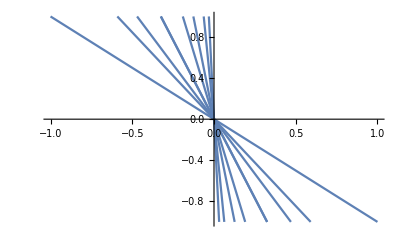

```mathematica
datapoints = {1,2,10,25,4,6,10, 17,14};
maxAngle = 45;
degPerUnit =- maxAngle/Max[datapoints];
unitToM[u_]:=Cot[degPerUnit*u*Pi/180];
Plot[Table[unitToM[datapoints[[u]]]*x,{u,1,Length[datapoints]}],{x,-1,1},PlotRange->1]
```

## Datenverarbeitung

Zuerst müssen die Daten importiert werden.

```mathematica
sh=Import[FileNameJoin[{NotebookDirectory[],"s-h.xlsx"}]];
ta=Import[FileNameJoin[{NotebookDirectory[],"Acc.csv"}]];
ts=Import[FileNameJoin[{NotebookDirectory[],"gps.xls"}]];
```

Von den gegebenen Daten brauchen wir nur Strecke-Höhe, Zeit-Beschleunigung und Zeit-Strecke Datenpunkte. Im nächsten Schritt filtern wir diese aus.

```mathematica
sh=Function[x,{x[[3]]/1000,x[[4]]}]/@Take[Flatten[sh,1],{2,Length[Flatten[sh,1]]-1}];
ta=Function[x,x[[{1,5}]]]/@Take[ta,{2,Length[ta]}];
ts=Function[x,x[[{1,8}]]]/@Take[Flatten[Take[ts,1],1],{2,-1}];
```

Nun wollen wir aber die Zeit-Beschleunigung und Zeit-Strecke Datenpunkte vereinen. Dazu nehmen wir alle 10 Sekunden die nähesten Beschleunigungs und Strecken Punkte.

```mathematica
dist[{u_,v_},{x_,y_}]:=Abs[u-x]
saFrom[t_]:={t,
Flatten[Nearest[ts,{t,0},DistanceFunction->dist],1][[2]],
Flatten[Nearest[ta,{t,0},DistanceFunction->dist],1][[2]]}
tsa=Table[saFrom[t],
{t,0,Max[First[Take[ts,-1]],First[Take[ta,-1]]],10}
];
```

## Von Strecke auf Höhe

Damit wir wissen auf welcher Höhe die Line liegen muss, brauchen wir eine Funktion, die unabhängig von den Datenpunkten einen korrekten Wert liefert. Da die Strecke zwischen den Datenpunkten durch eine Line verbunden wird, kann man mit den nähesten zwei Datenpunkte, welche rechts und links von der Eingabe s liegen, eine Geradengleichung aufstellen. Dadurch kann einfach die richtige Koordinate bestimmt werden.

```mathematica
h[s_]:=With[{p=SelectFirst[sh,First[#]>s&],q=SelectFirst[Reverse[sh],First[#]<s&]},
(p[[2]]-q[[2]])/(p[[1]]-q[[1]])(s-p[[1]])+p[[2]]
]
```

## Plotten des Graphen

Da wir nun wissen, wie man die Steigung und Höhe berechnen, muss nun noch geklärt werden, wie man die Geraden an den richtigen Punkt verschiebt. Der Punkt einer jeder Gerade ist gegeben durch die Höhe an der Strecke s, welche in tsa ist. 
Somit muss einfach nur der Punkt in eine Geradengleichung f(x)=m·x+t einsetzen. Man bekommt:

f(x)=m·x+t⇒^einsetzen h=m·s+t⇔t=h-m·s⇒f(x)=m·x+h-m·s=m(x-s)+h

Nun haben wir alle nötigen Sachen, um den Graph zu zeichnen:

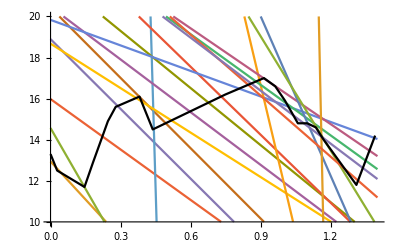

```mathematica
Table[
Cot[-maxAngle/Flatten[MaximalBy[tsa,Take[#,-1]&]][[3]]*tsa[[u]][[3]]*Pi/180]
*(x-tsa[[u]][[2]])+h[tsa[[u]][[2]]],
{u,1,103,5}];
Plot[%,{x,0,1.4},PlotRange->{{0,1.4},{10,20}}];
Show[%,ListLinePlot[sh,PlotStyle->Black]]
```

## Farben ändern

Nun soll sich die Farbe der Linien entsprechend der Beschleunigung/Steigung ändern.

## Blau→Kleinerer Winkel; Rot→Größerer Winkel

Beim kleinsten Beschleunigung soll die Farbe blau sein. Es soll die linear roter werden, während der Blauanteil linear kleiner wird. Bei einer Beschleunigung von max/2 soll die Farbe gleich (127.5, 0, 127.5) sein.

```mathematica
valuesLookedAt=Table[tsa[[u]][[3]],{u,1,103,5}];
maxLookedAt=Max[valuesLookedAt];
Table[
Plot[
Cot[-maxAngle/Flatten[MaximalBy[tsa,Take[#,-1]&]][[3]]*tsa[[u]][[3]]*Pi/180]
*(x-tsa[[u]][[2]])+h[tsa[[u]][[2]]], 
{x,0,1.4},
PlotRange->{{0,1.4},{10,20}},
ColorFunction->Function[x,RGBColor[tsa[[u]][[3]]/maxLookedAt,0,(maxLookedAt-tsa[[u]][[3]])/maxLookedAt]]], 
{u,1,103,5}];
Rasterize[Show[%,ListLinePlot[sh,PlotStyle->Black]],ImageResolution->300]
Table[RGBColor[tsa[[u]][[3]]/maxLookedAt,0,(maxLookedAt-tsa[[u]][[3]])/maxLookedAt],{u,1,103,5}]
```

{RGBColor[0.007544121155445359, 0, 0.9924558788445547],RGBColor[0.34075380368201275, 0, 0.6592461963179872],RGBColor[0.21340947209445751, 0, 0.7865905279055424],RGBColor[0.5131612348723684, 0, 0.4868387651276315],RGBColor[0.3719458390515235, 0, 0.6280541609484764],RGBColor[0.36905794944185033, 0, 0.6309420505581497],RGBColor[0.010939104569894728, 0, 0.9890608954301052],RGBColor[0.5812089620500882, 0, 0.4187910379499117],RGBColor[0.49113654456198064, 0, 0.5088634554380194],RGBColor[0.4535862927649628, 0, 0.5464137072350371],RGBColor[0.3814842368789019, 0, 0.618515763121098],RGBColor[1., 0, 0.],RGBColor[0.08802791847321875, 0, 0.9119720815267812],RGBColor[0.5398640239662614, 0, 0.46013597603373857],RGBColor[0.5116385791131954, 0, 0.48836142088680456],RGBColor[0.16293377284403981, 0, 0.8370662271559601],RGBColor[0.008060095814827032, 0, 0.9919399041851729],RGBColor[0.22756078683427622, 0, 0.7724392131657237],RGBColor[0.4245751389405842, 0, 0.5754248610594158],RGBColor[0.4886484856671962, 0, 0.5113515143328038],RGBColor[0.6770481996868726, 0, 0.32295180031312737]}

## Blau→Kleinerer Winkel; Rot→Größerer Winkel; Mit Übergang in Grün

Hier soll der Blauanteil maximal bei der kleinsten Beschleunigung sein und linear abnehmen, bis er bei einer Beschleunigung von max/2 gleich Null ist. In diesen Punkt soll nun der Rotanteil linear steigen, bis ein maximaler Rotanteil bei der maximalen Beschleunigung erreicht ist. Der Grünanteil soll linear startend vom der kleinsten Beschleunigung bei 0 bis zur Beschleunigung max/2 maximal ansteigen. Anschließnd soll der Grünanteil symmetrisch linear sinken.

```mathematica
valuesLookedAt=Table[tsa[[u]][[3]],{u,1,103,5}];
maxLookedAt=Max[valuesLookedAt];
Table[
Plot[
Cot[-maxAngle/Flatten[MaximalBy[tsa,Take[#,-1]&]][[3]]*tsa[[u]][[3]]*Pi/180]
*(x-tsa[[u]][[2]])+h[tsa[[u]][[2]]], 
{x,0,1.4},
PlotRange->{{0,1.4},{10,20}},
ColorFunction->Function[x,RGBColor[
If[tsa[[u]][[3]]/maxLookedAt>1/2,2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2],0],
-2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2]+1,
If[tsa[[u]][[3]]/maxLookedAt<1/2,2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2],0]
]
]
], 
{u,1,103,5}];
Rasterize[Show[%,ListLinePlot[sh,PlotStyle->Black]],ImageResolution->300]
Table[RGBColor[
If[tsa[[u]][[3]]/maxLookedAt>1/2,2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2],0],
-2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2]+1,
If[tsa[[u]][[3]]/maxLookedAt<1/2,2*Abs[tsa[[u]][[3]]/maxLookedAt-1/2],0]
],{u,1,103,5}]
```

-Graphics-

{RGBColor[0, 0.015088242310890676, 0.9849117576891093],RGBColor[0, 0.6815076073640255, 0.3184923926359745],RGBColor[0, 0.426818944188915, 0.573181055811085],RGBColor[0.026322469744736843, 0.9736775302552632, 0],RGBColor[0, 0.743891678103047, 0.256108321896953],RGBColor[0, 0.7381158988837007, 0.26188410111629934],RGBColor[0, 0.02187820913978944, 0.9781217908602106],RGBColor[0.16241792410017641, 0.8375820758998236, 0],RGBColor[0, 0.9822730891239613, 0.017726910876038726],RGBColor[0, 0.9071725855299256, 0.09282741447007437],RGBColor[0, 0.7629684737578037, 0.23703152624219626],RGBColor[1., 0., 0],RGBColor[0, 0.17605583694643756, 0.8239441630535624],RGBColor[0.07972804793252286, 0.9202719520674771, 0],RGBColor[0.02327715822639087, 0.9767228417736091, 0],RGBColor[0, 0.32586754568807963, 0.6741324543119204],RGBColor[0, 0.016120191629654057, 0.9838798083703459],RGBColor[0, 0.45512157366855244, 0.5448784263314476],RGBColor[0, 0.8491502778811684, 0.15084972211883163],RGBColor[0, 0.9772969713343924, 0.022703028665607583],RGBColor[0.35409639937374515, 0.6459036006262548, 0]}